```mathematica
(* Vandermonde, Lagrange Polynomials, Hermite Interpolation of same function *)

f[x_]:=3*x^3+x^2+2*x+10;
fprime[x_]=D[f[x],x];
xvec={-1,0,2,4};
yvec=f[xvec]
```

{6,10,42,226}

```mathematica
(* Vandermonde *)
mat={};
For[i=1,i≤Length[xvec],++i,
irow={};
For[j=1,j≤Length[xvec],++j,
If[j==1,
AppendTo[irow,1],
AppendTo[irow,xvec[[i]]^(j-1)]
];
];
AppendTo[mat,irow]
];
```

```mathematica
coef=LinearSolve[mat,yvec];
```

```mathematica
p[x_]=0;
For[i=1,i≤Length[coef],++i,
p[x]=coef[[i]]*x^(i-1)+p[x]
];
```

```mathematica
p[x]
```

10+2 x+x^2+3 x^3

```mathematica
f[x]
```

10+2 x+x^2+3 x^3

```mathematica
(* Lagrange *)
lpoly={};
For[i=1,i<=Length[xvec],++i,
Subscript[l, i][x_]=1;
For[j=1,j≤Length[xvec],++j,
If[j≠i,
Subscript[l, i][x_]=Subscript[l, i][x]*(x-xvec[[j]])/(xvec[[i]]-xvec[[j]])
];
];
AppendTo[lpoly,Subscript[l, i][x]]
];
```

```mathematica
q[x_]=0;
For[i=1,i≤Length[xvec],++i,
q[x_]=yvec[[i]]*lpoly[[i]]+q[x]
];
```

```mathematica
Sqrt[Integrate[(q[x]-f[x])^2,{x,-1,4}]]
```

0

```mathematica
Subscript[l, 1][x]
```

-1/15 (2-x) (4-x) x

```mathematica
lpoly
```

{-1/15 (2-x) (4-x) x,1/8 (2-x) (4-x) (1+x),1/12 (4-x) x (1+x),1/40 (-2+x) x (1+x)}

```mathematica
(* Hermite *)
hpoly={};
For[i=1,i≤Length[lpoly],++i,
Subscript[h, i][x_]=(Subscript[l, i][x])^2;
AppendTo[hpoly,Subscript[h, i][x]]
];
```

```mathematica
hpolyd={};
For[i=1,i≤Length[hpoly],++i,
Subscript[hprime, i][x_]=D[hpoly[[i]],x];
AppendTo[hpolyd,Subscript[hprime, i][x]]
];
```

```mathematica
Hpoly={};
For[i=1,i≤Length[hpoly],++i,
Subscript[H, i][x_]=(-Subscript[hprime, i][xvec[[i]]]*(x-xvec[[i]])+1)*Subscript[h, i][x];
AppendTo[Hpoly,Subscript[H, i][x]]
];
```

```mathematica
Spoly={};
For[i=1,i≤Length[hpoly],++i,
Subscript[S, i][x_]=(x-xvec[[i]])*Subscript[h, i][x];
AppendTo[Spoly,Subscript[S, i][x]]
];
```

```mathematica
h[x_]=0;
For[i=1,i≤Length[xvec],++i,
h[x_]=f[xvec[[i]]]*Subscript[H, i][x]+fprime[xvec[[i]]]*Subscript[S, i][x]+h[x]
];
```

```mathematica
xvec
yvec
```

{-1,0,2,4}

{6,10,42,226}

```mathematica
Hmat={};
For[i=1,i≤Length[xvec],++i,
irow={};
For[j=1,j≤Length[xvec],++j,
AppendTo[irow,Subscript[H, i][xvec[[j]]]
];
];
AppendTo[Hmat,irow]
];
```

```mathematica
Smat={};
For[i=1,i<+Length[xvec],++i,
irow={};
For[j=1,j≤Length[xvec],++j,
AppendTo[irow,Subscript[S, i][xvec[[j]]]
];
];
AppendTo[Smat,irow]
];
```

```mathematica
Hpolyd={};
For[i=1,i≤Length[Hpoly],++i,
Subscript[Hprime, i][x_]=D[Hpoly[[i]],x];
AppendTo[Hpolyd,Subscript[Hprime, i][x]]
];
```

```mathematica
Spolyd={};
For[i=1,i≤Length[Spoly],++i,
Subscript[Sprime, i][x_]=D[Spoly[[i]],x];
AppendTo[Spolyd,Subscript[Sprime, i][x]]
];
```

```mathematica
Hdmat={};
For[i=1,i≤Length[xvec],++i,
irow={};
For[j=1,j≤Length[xvec],++j,
AppendTo[irow,Subscript[Hprime, i][xvec[[j]]]]
];
AppendTo[Hdmat,irow]
];
```

```mathematica
Sdmat={};
For[i=1,i≤Length[xvec],++i,
irow={};
For[j=1,j≤Length[xvec],++j,
AppendTo[irow,Subscript[Sprime, i][xvec[[j]]]]
];
AppendTo[Sdmat,irow]
];
```

```mathematica
Sdmat
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

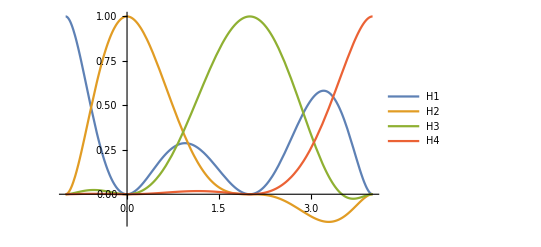

```mathematica
Plot[{Subscript[H, 1][x],Subscript[H, 2][x],Subscript[H, 3][x],Subscript[H, 4][x]},{x,-1,4},PlotLegends->{"H1","H2","H3","H4"}]
```

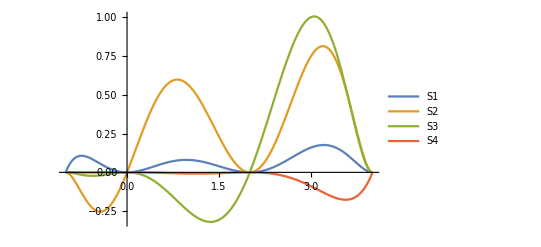

```mathematica
Plot[{Subscript[S, 1][x],Subscript[S, 2][x],Subscript[S, 3][x],Subscript[S, 4][x]},{x,-1,4},PlotLegends->{"S1","S2","S3","S4"}]
```

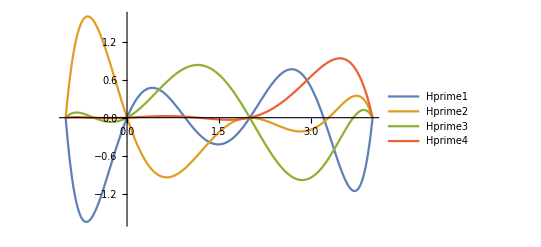

```mathematica
Plot[{Subscript[Hprime, 1][x],Subscript[Hprime, 2][x],Subscript[Hprime, 3][x],Subscript[Hprime, 4][x]},{x,-1,4},PlotLegends->{"Hprime1","Hprime2","Hprime3","Hprime4"}]
```

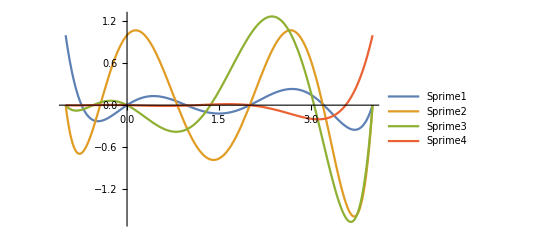

```mathematica
Plot[{Subscript[Sprime, 1][x],Subscript[Sprime, 2][x],Subscript[Sprime, 3][x],Subscript[Sprime, 4][x]},{x,-1,4},PlotLegends->{"Sprime1","Sprime2","Sprime3","Sprime4"}]
```